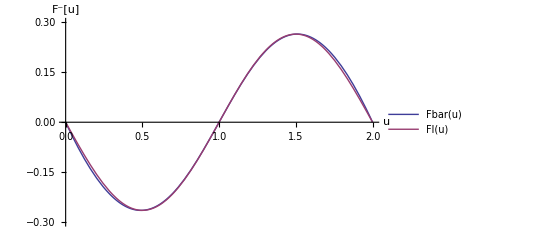

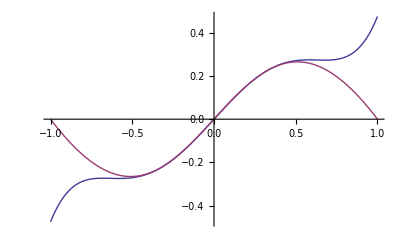

```mathematica
δ = 2;
L = 1;
k1 = 1;
l[u_] := √((L-u)^2+(δ/2)^2);
d = δ/(2L);
ψ[u_] := k1(l[u]-l[0])^2;
F[u_] := -ψ'[u];
Fbar[u_]:= F[u]/(k1 L);
Fs[u_]= Collect[Series[Fbar[u],{u,0,1}],u];
Fm[u_]= Collect[Series[Fbar[u+L],{u,0,5}],u];
Fl[u_]:=Fbar[L/2]Sin[π u];
Plot[{Fbar[u],Fl[u]},{u,0,2L},PlotRange->{-0.3,0.3},PlotLegends->"Expressions", AxesLabel->{"u","F^-[u]"}]
Plot[{Fm[u],Fbar[u+1]},{u,-1,1}]
```

```mathematica
N[Integrate[√ψ[u],{u,0,2}]]
```

0.53284

```mathematica
F[0.5]
```

-0.264911

```mathematica
(10 √2 0.53284)/0.1715
```

11.6399

```mathematica
x[v_]:=(10 √2*0.53284)/(√(10-v^2));
```

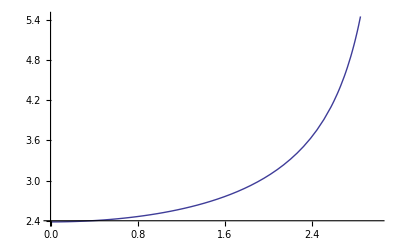

```mathematica
Plot[x[v],{v,0,3}]
```

```mathematica
x2[v_]:=20/(10-v^2)
```

4.43486

```mathematica
Solve[x[v]==8,v]
```

{{v→-3.01873},{v→3.01873}}

```mathematica
x[2.667]
```

1.17484

```mathematica
(2*x[2.667])^(1/2)
```

1.53287

```mathematica
N [ψ[1]]
```

0.171573

(-2+√5) u-(√5 u^3)/8+(3 √5 u^5)/128

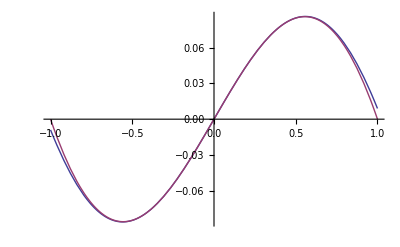

```mathematica
Fm[u]
```

```mathematica
FullSimplify[Fs[u]]
```

-u

```mathematica
Fm[u]
```

-u+(3 u^2)/4+(3 u^3)/8

```mathematica
Fl[u]
```

(2 (-√2+(√5)/2) Sin[π u])/(√5)

```mathematica
d=2
```

2

```mathematica
ϕo = A Exp[ⅈ σ] + Ab Exp[-ⅈ σ];
```

```mathematica
ϕ1 = 3 d^2/(1+d^2)A Ab - d^2/(2(1+d^2))A^2 Exp[ⅈ 2 σ] - d^2/(2(1+d^2))Ab^2 Exp[-ⅈ 2 σ];
```

```mathematica
FullSimplify[(d^2(d^2-4))/((1+d^2)^3)ϕo^3- 6 d^2/((1+d^2)^2)ϕo ϕ1]
```

48/125 ⅇ^(-3 ⅈ σ) (Ab+A ⅇ^(2 ⅈ σ)) (Ab^2-6 A Ab ⅇ^(2 ⅈ σ)+A^2 ⅇ^(4 ⅈ σ))

```mathematica
Ksp[u_]:= -Fbar'[u]
```

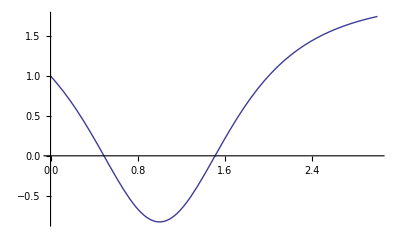

```mathematica
Plot[Ksp[u],{u,0,3}]
```

```mathematica
N[(8*10*√((2 √2)/(√5)-1))/(π √π)]
```

7.39461

```mathematica
7.39461/0.171573
```

43.0989

```mathematica
Integrate[√((1-y)^2+1),y]
```

1/2 ((-1+y) √(2-2 y+y^2)-ArcSinh[1-y])

```mathematica
Integrate[1/(√((1-x)^2+d1^2)-lo),x]
```

(lo ArcTan[(-1+x)/(√(d1^2-lo^2))])/(√(d1^2-lo^2))+(lo ArcTan[(lo (-1+x))/(√(d1^2-lo^2) √(d1^2+(-1+x)^2))])/(√(d1^2-lo^2))+Log[-1+√(d1^2+(-1+x)^2)+x]

```mathematica
FullSimplify[ArcSinh[1-x]]
```

```mathematica
TrigToExp[ArcTan[x]]
```

1/2 ⅈ Log[1-ⅈ x]-1/2 ⅈ Log[1+ⅈ x]

```mathematica
FullSimplify[D[-ArcSinh[1-x]+1/(√2)(2 Log[2-x]-2 Log[x]+Log[2-x+√2 √(2-2 x+x^2)]-Log[x+√2 √(2-2 x+x^2)]),x]]
```

1/(-√2+√(2+(-2+x) x))

```mathematica
TrigToExp[(lo ArcTan[(-1+x)/(√(d1^2-lo^2))])/(√(d1^2-lo^2))+(lo ArcTan[(lo (-1+x))/(√(d1^2-lo^2) √(d1^2+(-1+x)^2))])/(√(d1^2-lo^2))]
```

(ⅈ lo Log[1-(ⅈ (-1+x))/(√(d1^2-lo^2))])/(2 √(d1^2-lo^2))-(ⅈ lo Log[1+(ⅈ (-1+x))/(√(d1^2-lo^2))])/(2 √(d1^2-lo^2))+(ⅈ lo Log[1-(ⅈ lo (-1+x))/(√(d1^2-lo^2) √(d1^2+(-1+x)^2))])/(2 √(d1^2-lo^2))-(ⅈ lo Log[1+(ⅈ lo (-1+x))/(√(d1^2-lo^2) √(d1^2+(-1+x)^2))])/(2 √(d1^2-lo^2))

```mathematica
FullSimplify[(lo Log[1-(-1+x)/(√(-d1^2+lo^2))])/(2 √(-d1^2+lo^2))-(lo Log[1+(-1+x)/(√(-d1^2+lo^2))])/(2 √(-d1^2+lo^2))+(lo Log[1-(lo (-1+x))/(√(-d1^2+lo^2) √(d1^2+(-1+x)^2))])/(2 √(-d1^2+lo^2))-(lo Log[1+(lo (-1+x))/(√(-d1^2+lo^2) √(d1^2+(-1+x)^2))])/(2 √(-d1^2+lo^2))]
```

```mathematica
Clear[a,b]
```

```mathematica
a = (-1+x)/(√(lo^2-d1^2));
b = (lo (-1+x))/(√(lo^2-d1^2) √(d1^2+(-1+x)^2));
```

```mathematica
FullSimplify[((1-a)/(1+a))((1-b)/(1+b))]
```

```mathematica
s[lo_,d1_]:=((1+√(-d1^2+lo^2)-x) (lo+√(-d1^2+lo^2) √(d1^2+(-1+x)^2)-lo x))/((√(-d1^2+lo^2) √(d1^2+(-1+x)^2)+lo (-1+x)) (-1+√(-d1^2+lo^2)+x))
```

```mathematica
-1+√(d1^2+(-1+x)^2)+x
```

```mathematica
s[√2,1]
```

((2-x) (√2+√(1+(-1+x)^2)-√2 x))/((√(1+(-1+x)^2)+√2 (-1+x)) x)

```mathematica
Clear[a,b]
```

```mathematica
a[x_] := (-1+x)/(√(lo^2-d1^2));
b[x_] := (lo (-1+x))/(√(lo^2-d1^2) √(d1^2+(-1+x)^2));
```

```mathematica
lo=√2;
d1=1;
co=√10;
v=2.667;
```

```mathematica
z[x_]:=√((co^2-v^2)/2)Log[(1-a[x])/(1+a[x])(1-b[x])/(1+b[x])(x-1+√((x-1)^2+d^2))^((2 √(lo^2-d^2))/lo)]
```

```mathematica
N[z[0]]
```

∞

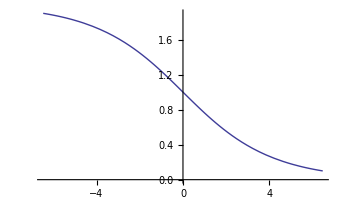

```mathematica
ParametricPlot[{z[x],x},{x,0.1,1.9}]
```